## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.7, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL07=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.7)
```

0.699871

```mathematica
Zprime10decayfixedmass07[CvR_]:=MassZprime10/(12π)(1/4(CvL07+CvR)^2+1/4(CvL07-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL07+CvR)^2-1/2(CvL07+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass07Table=Table[{Q[i],Zprime10decayfixedmass07[Q[i]]},{i,0,Npt}]
```

{{0.,64.9448},{0.1,66.2689},{0.2,70.2447},{0.3,76.8723},{0.4,86.1517},{0.5,98.0829},{0.6,112.666},{0.7,129.901},{0.8,149.787},{0.9,172.325},{1.,197.516}}

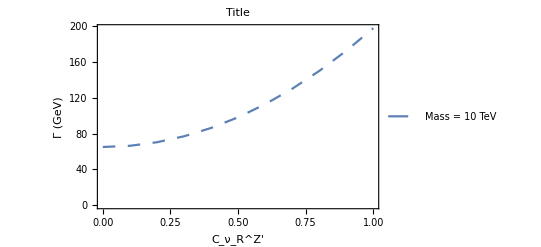

```mathematica
PlotZprimeDecayFixed1007=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

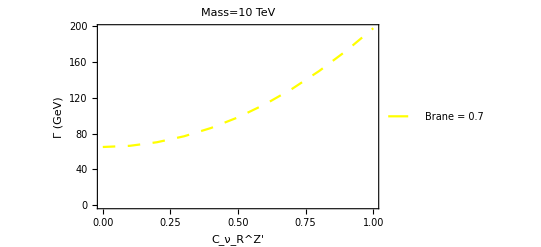

```mathematica
PlotZprimeDecayFixed1007B=ListPlot[%%, Joined-> True,PlotStyle->{Yellow,Dashing[Medium]},PlotLegends->{"Brane = 0.7"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass07Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 64.9448
0.1 | 66.2689
0.2 | 70.2447
0.3 | 76.8723
0.4 | 86.1517
0.5 | 98.0829
0.6 | 112.666
0.7 | 129.901
0.8 | 149.787
0.9 | 172.325
1. | 197.516

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.7, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL07=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.7)
```

0.699871

```mathematica
Zprime8decayfixedmass07[CvR_]:=MassZprime8/(12π)(1/4(CvL07+CvR)^2+1/4(CvL07-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL07+CvR)^2-1/2(CvL07+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass07Table=Table[{Q[i],Zprime8decayfixedmass07[Q[i]]},{i,0,Npt}]
```

{{0.,51.9471},{0.1,53.0053},{0.2,56.1846},{0.3,61.485},{0.4,68.9064},{0.5,78.4489},{0.6,90.1125},{0.7,103.897},{0.8,119.803},{0.9,137.83},{1.,157.977}}

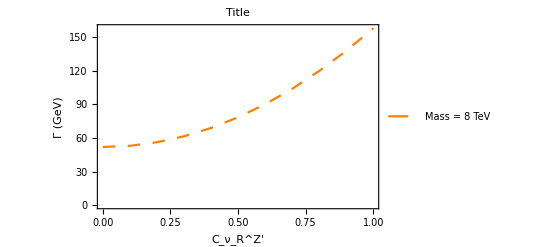

```mathematica
PlotZprimeDecayFixed807=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

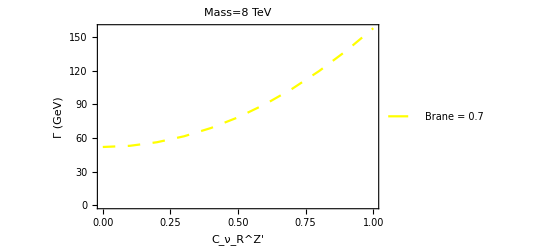

```mathematica
PlotZprimeDecayFixed807B=ListPlot[%%, Joined-> True,PlotStyle->{Yellow,Dashing[Medium]},PlotLegends->{"Brane = 0.7"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass07Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 51.9471
0.1 | 53.0053
0.2 | 56.1846
0.3 | 61.485
0.4 | 68.9064
0.5 | 78.4489
0.6 | 90.1125
0.7 | 103.897
0.8 | 119.803
0.9 | 137.83
1. | 157.977

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.7, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL07=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.7)
```

0.699871

```mathematica
Zprime5decayfixedmass07[CvR_]:=MassZprime5/(12π)(1/4(CvL07+CvR)^2+1/4(CvL07-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL07+CvR)^2-1/2(CvL07+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass07Table=Table[{Q[i],Zprime5decayfixedmass07[Q[i]]},{i,0,Npt}]
```

{{0.,32.4432},{0.1,33.1018},{0.2,35.0852},{0.3,38.3932},{0.4,43.0259},{0.5,48.9834},{0.6,56.2655},{0.7,64.8724},{0.8,74.8039},{0.9,86.0601},{1.,98.6411}}

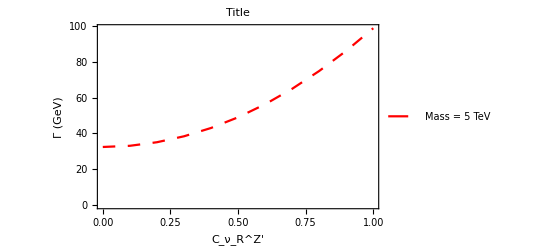

```mathematica
PlotZprimeDecayFixed507=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

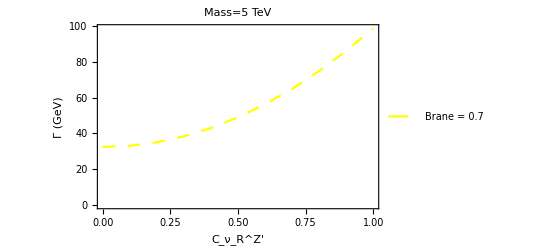

```mathematica
PlotZprimeDecayFixed507B=ListPlot[%%, Joined-> True,PlotStyle->{Yellow,Dashing[Medium]},PlotLegends->{"Brane = 0.7"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass07Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 32.4432
0.1 | 33.1018
0.2 | 35.0852
0.3 | 38.3932
0.4 | 43.0259
0.5 | 48.9834
0.6 | 56.2655
0.7 | 64.8724
0.8 | 74.8039
0.9 | 86.0601
1. | 98.6411

## OverLay

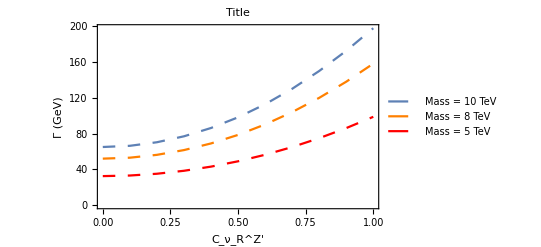

```mathematica
Show[PlotZprimeDecayFixed1007,PlotZprimeDecayFixed807,PlotZprimeDecayFixed507]
```

## OverLay 2

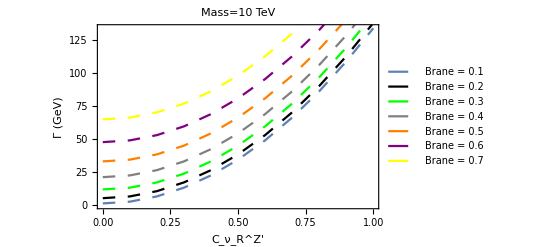

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B,PlotZprimeDecayFixed1006B,PlotZprimeDecayFixed1007B]
```

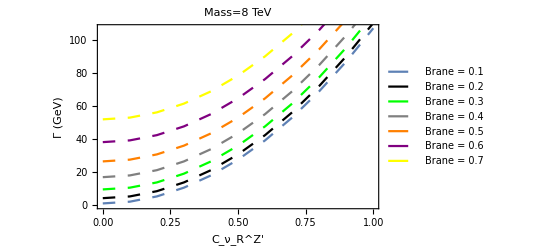

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B,PlotZprimeDecayFixed806B,PlotZprimeDecayFixed807B]
```

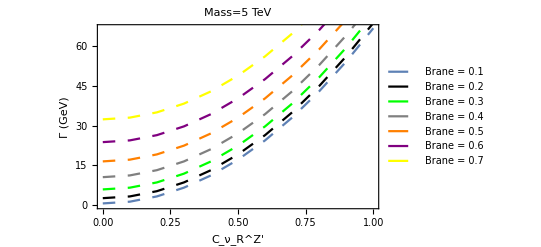

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B,PlotZprimeDecayFixed506B,PlotZprimeDecayFixed507B]
```